Kevin Daily

There’s a grid of functions that players pick from which are then used. A player must click a vertex then click a function to extend the graph the goal is to make the largest graph

## Helper Functions

```mathematica
(* construct a vertex with id, label, and click action *)
vert[id_,label_,action_]:=Button[Labeled[id,label],action[0]]
```

```mathematica
(* create grid cell with selectable functions *)
cell[fnHead_,clickAction_]:=ClickPane[Mouseover[fnHead,Style[fnHead,FontColor->Orange]],clickAction]
```

```mathematica
arg[arg_]:=(argumentSelected=arg)
```

```mathematica
funct[fn_]:=(functionSelected=fn)
```

```mathematica
(* result, boolean *)
eval[fn_,arg_,expected_]:={fn@arg,TrueQ[Head[arg]==expected]}
```

## Init

```mathematica
argumentSelected=Null;
functionSelected=Null;
```

## Display

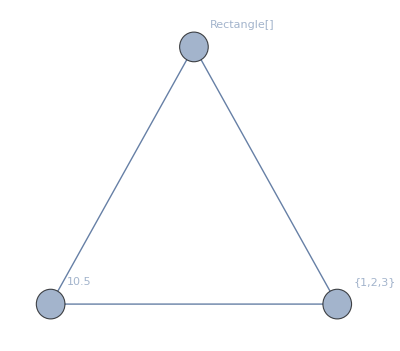

```mathematica
Graph[
{
vert[1,"10.5",x↦arg[10.5]], 
vert[2,"{1,2,3}",x↦arg[{1,2,3}]], 
vert[3,"Rectangle[]",x↦arg[Rectangle[]]]
},
{1<->2,2<->3,3<->1}, VertexSize->Small]
```

```mathematica
Grid[{
{
cell[Sin,x↦funct[Sin],Real],
cell[Cos,x↦funct[Cos],Real],
cell[Tan,x↦funct[Tan], Real]
},
{
cell[Map,x↦funct[Map], List],
cell[Array,x↦funct[Array], List],
cell[Range,x↦funct[Range], List]
},
{
cell[Fold,x↦funct[Fold],Number],
cell[Nest,x↦funct[Nest]],
cell[Select,x↦funct[Select]]
}
}, 
Frame->All]
```

|  | 
 |  | 
 |  |

## Selected

```mathematica
Dynamic[argumentSelected]
```

```mathematica
Dynamic[functionSelected]
```

## Submit

```mathematica
Button["Evaluate",eval[First[functionSelected],argumentSelected,functionSelected[[2]]]]
```

Evaluate

```mathematica
TrueQ[Head[5.5]==Integer]
```

False

```mathematica
Range
```

The problem is that functions can often take any argument and will evaluate to a symbolic expression instead of throwing an error. I tried to indicate what the output should be but functions like nest can be a number or list. Thus, the problem of executing an arbitrary function with an argument is equivalent to the presentation we had on same checking. The solution is to simplify the game until players are just dealing with integers and list with a small set of function and its not fun

```mathematica
Grid[{
{3.5,"open","open","open","open"},
{3,"open","open","open","open"},
{1,"open","open","open","open"},
{9,"open","open","open","open"},
{11,"open","open","open","open"}
},Frame->All, ItemSize->5,Spacings->{3,3}]
```

3.5 | open | open | open | open
3 | open | open | open | open
1 | open | open | open | open
9 | open | open | open | open
11 | open | open | open | open

```mathematica
board=Array[RandomInteger[9]&,{5,5}]
```

{{3,2,0,0,7},{1,2,4,0,5},{1,4,0,9,1},{0,1,2,6,0},{1,5,0,9,6}}

```mathematica
Dynamic[Style[Grid[board,Frame->All,ItemSize->5,Spacings->{1,2}],FontSize->20]]
```

```mathematica
ClickPane[Mouseover[Style[Sin,FontSize->30],Style[Sin,Background->Orange,FontSize->30]],Echo["sam"]&]
```